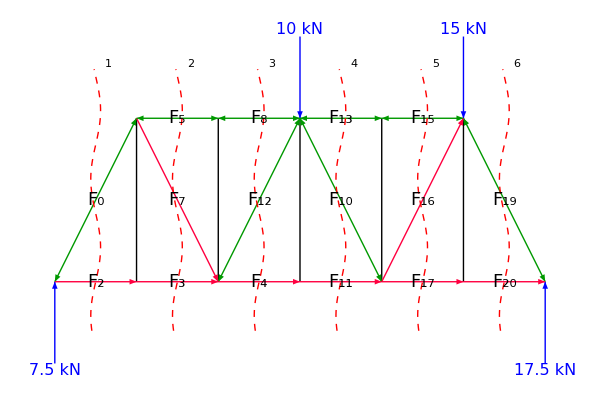

```mathematica
Module[{w,h,FD,FF,sol,RA,RG,colC,colT},
w=5;h=5;FD=10;FF=15;

sol=Quiet@Solve[{3*w*FD+5*w*FF-6*w*rg==0,ra-FD-FF+rg==0},{ra,rg}][[1]];
RA=ra/.sol;RG=rg/.sol;

colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Graphics[{Thick,
Line[{{#*w,0},{#*w,h}}]&/@Range@5,

{Blue,Arrow[{{3*w,1.5*h},{3*w,h}}],Arrow[{{5*w,1.5*h},{5*w,h}}],Text[Style[Row@{#1," kN"},16],#2,{0,-1.5}]&@@@{{FD,{3*w,1.5*h}},{FF,{5*w,1.5*h}}},
Arrow[{{0,-0.5*h},{0,0}}],Arrow[{{6*w,-0.5*h},{6*w,0}}],Text[Style[Row@{N@#1," kN"},16],#2,{0,1.5}]&@@@{{RA,{0,-0.5*h}},{RG,{6*w,-0.5*h}}}},

{colC,Arrowheads@{-0.035,0.035},
Arrow[{{0,0},{w,h}}],Arrow[{{w,h},{2*w,h}}],Arrow[{{2*w,h},{3*w,h}}],Arrow[{{3*w,h},{4*w,h}}],Arrow[{{4*w,h},{5*w,h}}],Arrow[{{5*w,h},{6*w,0}}],Arrow[{{2*w,0},{3*w,h}}],Arrow[{{3*w,h},{4*w,0}}]},

{colT,Arrowheads@{{0.035,0.325},{-0.035,0.675}},
Arrow[{{0,0},{w,0}}],Arrow[{{w,0},{2*w,0}}],Arrow[{{2*w,0},{3*w,0}}],Arrow[{{3*w,0},{4*w,0}}],Arrow[{{4*w,0},{5*w,0}}],Arrow[{{5*w,0},{6*w,0}}],Arrow[{{w,h},{2*w,0}}],Arrow[{{4*w,0},{5*w,h}}]},

Table[{
{Dashed,Red,Line[{0.3*Sin[1.5*#]+w*(i+0.5),#}&/@Range[-0.3*h,1.3*h,0.1]]},
Text[Framed[Style[Row@{" ",i+1," "},17],RoundingRadius->15],{w*(i+0.7),1.3*h},{1,-1}]},{i,0,5}],

Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{
{0,{0.5*w,0.5*h}},{2,{0.5*w,0}},{3,{1.5*w,0}},{4,{2.5*w,0}},{5,{1.5*w,h}},{7,{1.5*w,0.5*h}},{8,{2.5*w,h}},{10,{3.5*w,0.5*h}},{11,{3.5*w,0}},{12,{2.5*w,0.5*h}},{13,{3.5*w,h}},{15,{4.5*w,h}},{16,{4.5*w,0.5*h}},{17,{4.5*w,0}},{19,{5.5*w,0.5*h}},{20,{5.5*w,0}}}
},ImageSize->{600,400}]
]
```

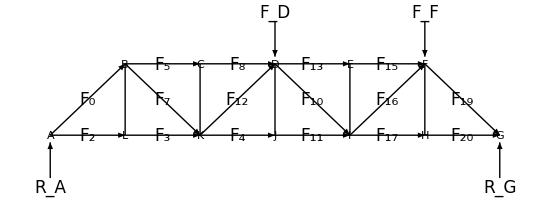

```mathematica
Module[{w,h,FD,FF,δ,sol,RA,RG,colC,colT},
w=5;h=5;FD=10;FF=15;δ=0.6*h;

sol=Quiet@Solve[{3*w*FD+5*w*FF-6*w*rg==0,ra-FD-FF+rg==0},{ra,rg}][[1]];
RA=ra/.sol;RG=rg/.sol;

colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Graphics[{Thick,
Line[{{#*w,0},{#*w,h}}]&/@Range@5,

Arrow[{{3*w,h+δ},{3*w,1.1*h}}],Arrow[{{5*w,h+δ},{5*w,1.1*h}}],Text[Style[Subscript[Style["F",Italic],#1],17],#2,{0,-1.5}]&@@@{{"D",{3*w,h+δ}},{"F",{5*w,h+δ}}},
Arrow[{{0,-δ},{0,-0.1*h}}],Arrow[{{6*w,-δ},{6*w,-0.1*h}}],Text[Style[Subscript[Style["R",Italic],#1],17],#2,{0,1.5}]&@@@{{"A",{0,-δ}},{"G",{6*w,-δ}}},

{Arrowheads@{{-0.035,0.1},{0.035,0.9}},
Arrow[{{0,0},{w,h}}],Arrow[{{w,h},{2*w,h}}],Arrow[{{2*w,h},{3*w,h}}],Arrow[{{3*w,h},{4*w,h}}],Arrow[{{4*w,h},{5*w,h}}],Arrow[{{5*w,h},{6*w,0}}],Arrow[{{2*w,0},{3*w,h}}],Arrow[{{3*w,h},{4*w,0}}]},

{Arrowheads@{{0.035,0.4},{-0.035,0.6}},
Arrow[{{0,0},{w,0}}],Arrow[{{w,0},{2*w,0}}],Arrow[{{2*w,0},{3*w,0}}],Arrow[{{3*w,0},{4*w,0}}],Arrow[{{4*w,0},{5*w,0}}],Arrow[{{5*w,0},{6*w,0}}],Arrow[{{w,h},{2*w,0}}],Arrow[{{4*w,0},{5*w,h}}]},

Text[Style[Subscript[Style["F",Italic],#1],17,Background->White],#2]&@@@{
{0,{0.5*w,0.5*h}},{2,{0.5*w,0}},{3,{1.5*w,0}},{4,{2.5*w,0}},{5,{1.5*w,h}},{7,{1.5*w,0.5*h}},{8,{2.5*w,h}},{10,{3.5*w,0.5*h}},{11,{3.5*w,0}},{12,{2.5*w,0.5*h}},{13,{3.5*w,h}},{15,{4.5*w,h}},{16,{4.5*w,0.5*h}},{17,{4.5*w,0}},{19,{5.5*w,0.5*h}},{20,{5.5*w,0}}},

Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->15,Background->White,FrameMargins->Small],#2]&@@@{
{"A",{0,0}},{"B",{w,h}},{"C",{2*w,h}},{"D",{3*w,h}},{"E",{4*w,h}},{"F",{5*w,h}},{"G",{6*w,0}},{"H",{5*w,0}},{" I ",{4*w,0}},{"J",{3*w,0}},{"K",{2*w,0}},{"L",{w,0}}}
},ImageSize->550]
]
```

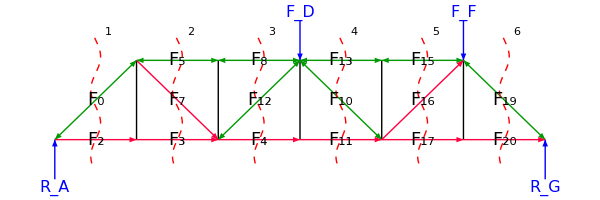

```mathematica
Module[{w,h,FD,FF,sol,RA,RG,colC,colT},
w=5;h=5;FD=10;FF=15;

sol=Quiet@Solve[{3*w*FD+5*w*FF-6*w*rg==0,ra-FD-FF+rg==0},{ra,rg}][[1]];
RA=ra/.sol;RG=rg/.sol;

colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Graphics[{Thick,
Line[{{#*w,0},{#*w,h}}]&/@Range@5,

{Blue,Arrow[{{3*w,1.5*h},{3*w,h}}],Arrow[{{5*w,1.5*h},{5*w,h}}],Text[Style[Subscript[Style["F",Italic],#1],16],#2,{0,-1.5}]&@@@{{"D",{3*w,1.5*h}},{"F",{5*w,1.5*h}}},
Arrow[{{0,-0.5*h},{0,0}}],Arrow[{{6*w,-0.5*h},{6*w,0}}],Text[Style[Subscript[Style["R",Italic],#1],16],#2,{0,1.5}]&@@@{{"A",{0,-0.5*h}},{"G",{6*w,-0.5*h}}}},

{colC,Arrowheads@{-0.035,0.035},
Arrow[{{0,0},{w,h}}],Arrow[{{w,h},{2*w,h}}],Arrow[{{2*w,h},{3*w,h}}],Arrow[{{3*w,h},{4*w,h}}],Arrow[{{4*w,h},{5*w,h}}],Arrow[{{5*w,h},{6*w,0}}],Arrow[{{2*w,0},{3*w,h}}],Arrow[{{3*w,h},{4*w,0}}]},

{colT,Arrowheads@{{0.035,0.325},{-0.035,0.675}},
Arrow[{{0,0},{w,0}}],Arrow[{{w,0},{2*w,0}}],Arrow[{{2*w,0},{3*w,0}}],Arrow[{{3*w,0},{4*w,0}}],Arrow[{{4*w,0},{5*w,0}}],Arrow[{{5*w,0},{6*w,0}}],Arrow[{{w,h},{2*w,0}}],Arrow[{{4*w,0},{5*w,h}}]},

Table[{
{Dashed,Red,Line[{0.3*Sin[1.5*#]+w*(i+0.5),#}&/@Range[-0.3*h,1.3*h,0.1]]},
Text[Framed[Style[Row@{" ",i+1," "},17],RoundingRadius->15],{w*(i+0.7),1.3*h},{1,-1}]},{i,0,5}],

Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{
{0,{0.5*w,0.5*h}},{2,{0.5*w,0}},{3,{1.5*w,0}},{4,{2.5*w,0}},{5,{1.5*w,h}},{7,{1.5*w,0.5*h}},{8,{2.5*w,h}},{10,{3.5*w,0.5*h}},{11,{3.5*w,0}},{12,{2.5*w,0.5*h}},{13,{3.5*w,h}},{15,{4.5*w,h}},{16,{4.5*w,0.5*h}},{17,{4.5*w,0}},{19,{5.5*w,0.5*h}},{20,{5.5*w,0}}}
},ImageSize->600]
]
```